# Spin state of Dirac cone

## Actual tinkering

We have the Hamiltonian  with eigenvalues . Wish to find the eigenstates and their spin expectation value.
Assume  where  is some normalization.
By the time independent Schrodinger equation, we find

```mathematica
k={kx, ky, kz}
```

{kx,ky,kz}

```mathematica
(H=s v Sum[PauliMatrix[i] k[[i]], {i, 3}] )//MatrixForm
```

(kz s v | (kx-ⅈ ky) s v
(kx+ⅈ ky) s v | -kz s v)

```mathematica
Engy=sgn v Norm[k]
```

sgn v √(Abs[kx]^2+Abs[ky]^2+Abs[kz]^2)

Take the spin part of the Schrodinger equation

```mathematica
eq=Refine[H.{1, b}  ==Engy * {1, b}, {kx, ky, kz}∈Reals]
```

{b (kx-ⅈ ky) s v+kz s v,(kx+ⅈ ky) s v-b kz s v}=={√(kx^2+ky^2+kz^2) sgn v,b √(kx^2+ky^2+kz^2) sgn v}

```mathematica
bs=Table[
Solve[eq, b]/.{s->s, sgn->sgn},
{s, {1,-1}}, {sgn, {1, -1}}
]//Flatten
```

{b→-(kz-√(kx^2+ky^2+kz^2))/(kx-ⅈ ky),b→-(kz+√(kx^2+ky^2+kz^2))/(kx-ⅈ ky),b→-(kz+√(kx^2+ky^2+kz^2))/(kx-ⅈ ky),b→-(kz-√(kx^2+ky^2+kz^2))/(kx-ⅈ ky)}

```mathematica
bs =DeleteDuplicates[bs]
```

{b→-(kz-√(kx^2+ky^2+kz^2))/(kx-ⅈ ky),b→-(kz+√(kx^2+ky^2+kz^2))/(kx-ⅈ ky)}

We have thus found the spin part, and we go on to normalization.
’
The plane wave is already normalized, so need only consider spin part.
They are trivial, and the result is

Find the components of the spin expectation value

```mathematica
component[n_, b_]:=FullSimplify[
Refine[Conjugate[{1,b}] .PauliMatrix[n] .{1,b} /(1+Conjugate[b] b), {kx, ky, kz}∈Reals]
]
```

```mathematica
Table[
component[i, b/.First[bs]],
{i, 3}
]
```

{kx/(√(kx^2+ky^2+kz^2)),ky/(√(kx^2+ky^2+kz^2)),kz/(√(kx^2+ky^2+kz^2))}

Verity that the two solutions are orthonormal

```mathematica
Refine[
(Conjugate[{1,b}]/.First[bs]).({1,b}/.Last[bs]),
{kx, ky, kz}∈Reals
]
```

1+((kz-√(kx^2+ky^2+kz^2)) (kz+√(kx^2+ky^2+kz^2)))/((kx-ⅈ ky) (kx+ⅈ ky))

```mathematica
Simplify[1+((kz-√(kx^2+ky^2+kz^2)) (kz+√(kx^2+ky^2+kz^2)))/((kx-ⅈ ky) (kx+ⅈ ky))]
```

0

Yes, they are orthogonal

```mathematica
bs
```

{b→-(kz-√(kx^2+ky^2+kz^2))/(kx-ⅈ ky),b→-(kz+√(kx^2+ky^2+kz^2))/(kx-ⅈ ky)}

```mathematica
Refine[
Conjugate[{1,b}].{1,b}/(1+Conjugate[b]b)/.bs,
{kx, ky, kz}∈Reals
]
```

1

## Initial tinkering

```mathematica
b=(k-kz)/(kx - I ky)
```

(k-kz)/(kx-ⅈ ky)

```mathematica
%/.{k->Sqrt[x^2 + y^2 + z^2], kx->x, ky->y, kz->z}
```

(-z+√(x^2+y^2+z^2))/(x-ⅈ y)

```mathematica
% * Conjugate[%]
```

((-z+√(x^2+y^2+z^2)) (-Conjugate[z]+Conjugate[√(x^2+y^2+z^2)]))/((x-ⅈ y) (Conjugate[x]+ⅈ Conjugate[y]))

```mathematica
Refine[%, {x, y, z}∈Reals]
```

((-z+√(x^2+y^2+z^2))^2)/((x-ⅈ y) (x+ⅈ y))

```mathematica
Simplify[((-z+√(x^2+y^2+z^2))^2)/((x-ⅈ y) (x+ⅈ y))]
```

((z-√(x^2+y^2+z^2))^2)/(x^2+y^2)

```mathematica
1/(1+%)
```

1/(1+((z-√(x^2+y^2+z^2))^2)/(x^2+y^2))

```mathematica
FullSimplify[1/(1+((z-√(x^2+y^2+z^2))^2)/(x^2+y^2))]
```

1/2 (1+z/(√(x^2+y^2+z^2)))

```mathematica
cartToPolar={kx->k Cos[θ] Sin[ϕ], ky->k Sin[θ] Sin[ϕ], kz->k Cos[ϕ]}
```

{kx→k Cos[θ] Sin[ϕ],ky→k Sin[θ] Sin[ϕ],kz→k Cos[ϕ]}

```mathematica
1 + 2 kz (kz-k)/(kx^2 + ky^2)/.cartToPolar
```

1+(2 k Cos[ϕ] (-k+k Cos[ϕ]))/(k^2 Cos[θ]^2 Sin[ϕ]^2+k^2 Sin[θ]^2 Sin[ϕ]^2)

```mathematica
TrigReduce[1+(2 k Cos[ϕ] (-k+k Cos[ϕ]))/(k^2 Cos[θ]^2 Sin[ϕ]^2+k^2 Sin[θ]^2 Sin[ϕ]^2)]
```

(Csc[ϕ]^2 (1-2 Cos[ϕ]+Cos[2 ϕ]+Cos[θ]^2 Sin[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))/(Cos[θ]^2+Sin[θ]^2)

```mathematica
Simplify[(Csc[ϕ]^2 (1-2 Cos[ϕ]+Cos[2 ϕ]+Cos[θ]^2 Sin[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))/(Cos[θ]^2+Sin[θ]^2)]
```

Tan[ϕ/2]^2

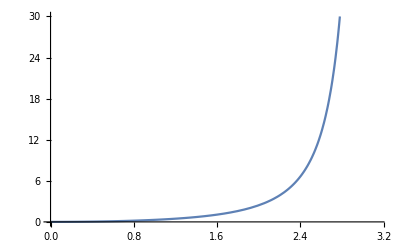

```mathematica
Plot[%, {ϕ, 0, Pi}]
```

```mathematica
{1, b}.{1,b}
```

1+(k-kz)^2/(kx-ⅈ ky)^2

```mathematica
ConjugateTranspose[{1, b}]
```

{1,(k-kz)/(kx-ⅈ ky)}

```mathematica
{1,b}
```

{1,(k-kz)/(kx-ⅈ ky)}

```mathematica
Conjugate[{1,b}]
```

{1,(Conjugate[k]-Conjugate[kz])/(Conjugate[kx]+ⅈ Conjugate[ky])}

```mathematica
Conjugate[{1,b}] .PauliMatrix[3] .{1,b}
```

1-((k-kz) (Conjugate[k]-Conjugate[kz]))/((kx-ⅈ ky) (Conjugate[kx]+ⅈ Conjugate[ky]))

```mathematica
Refine[%, {k, kx, ky, kz}∈Reals]
```

1-(k-kz)^2/((kx-ⅈ ky) (kx+ⅈ ky))

```mathematica
Simplify[1-(k-kz)^2/((kx-ⅈ ky) (kx+ⅈ ky))]
```

1-(k-kz)^2/(kx^2+ky^2)

```mathematica
%/.k->Sqrt[kx^2 + ky^2 + kz^2]
```

1-((-kz+√(kx^2+ky^2+kz^2))^2)/(kx^2+ky^2)

```mathematica
Simplify[1-((-kz+√(kx^2+ky^2+kz^2))^2)/(kx^2+ky^2)]
```

(2 kz (-kz+√(kx^2+ky^2+kz^2)))/(kx^2+ky^2)

```mathematica
% * 1/(1+Conjugate[b] b)
```

(2 kz (-kz+√(kx^2+ky^2+kz^2)))/((kx^2+ky^2) (1+((k-kz) (Conjugate[k]-Conjugate[kz]))/((kx-ⅈ ky) (Conjugate[kx]+ⅈ Conjugate[ky]))))

```mathematica
Refine[%, {k, kx, ky, kz}∈Reals]
```

(2 kz (-kz+√(kx^2+ky^2+kz^2)))/((kx^2+ky^2) (1+(k-kz)^2/((kx-ⅈ ky) (kx+ⅈ ky))))

```mathematica
FullSimplify[(2 kz (-kz+√(kx^2+ky^2+kz^2)))/((kx^2+ky^2) (1+(k-kz)^2/((kx-ⅈ ky) (kx+ⅈ ky))))]
```

(2 kz (-kz+√(kx^2+ky^2+kz^2)))/(kx^2+ky^2+(k-kz)^2)

```mathematica
%/.k->Sqrt[kx^2 + ky^2+kz^2]
```

```mathematica
{a, c}.{a,c}
```

a^2+c^2

(2 kz (-kz+√(kx^2+ky^2+kz^2)))/(kx^2+ky^2+(-kz+√(kx^2+ky^2+kz^2))^2)

```mathematica
FullSimplify[(2 kz (-kz+√(kx^2+ky^2+kz^2)))/(kx^2+ky^2+(-kz+√(kx^2+ky^2+kz^2))^2)]
```

kz/(√(kx^2+ky^2+kz^2))

```mathematica
Refine[Conjugate[{1,b}] .PauliMatrix[1] .{1,b}/.k->Sqrt[kx^2 + ky^2 + kz^2], {k, kx, ky, kz}∈Reals]
```

(-kz+√(kx^2+ky^2+kz^2))/(kx-ⅈ ky)+(-kz+√(kx^2+ky^2+kz^2))/(kx+ⅈ ky)

```mathematica
Simplify[(-kz+√(kx^2+ky^2+kz^2))/(kx-ⅈ ky)+(-kz+√(kx^2+ky^2+kz^2))/(kx+ⅈ ky)]
```

(2 kx (-kz+√(kx^2+ky^2+kz^2)))/(kx^2+ky^2)

```mathematica
% * Refine[1/(1+Conjugate[b] b)/.k->Sqrt[kx^2 + ky^2 + kz^2], {k, kx, ky, kz}∈Reals]
```

(2 kx (-kz+√(kx^2+ky^2+kz^2)))/((kx^2+ky^2) (1+((-kz+√(kx^2+ky^2+kz^2))^2)/((kx-ⅈ ky) (kx+ⅈ ky))))

```mathematica
FullSimplify[(2 kx (-kz+√(kx^2+ky^2+kz^2)))/((kx^2+ky^2) (1+((-kz+√(kx^2+ky^2+kz^2))^2)/((kx-ⅈ ky) (kx+ⅈ ky))))]
```

kx/(√(kx^2+ky^2+kz^2))

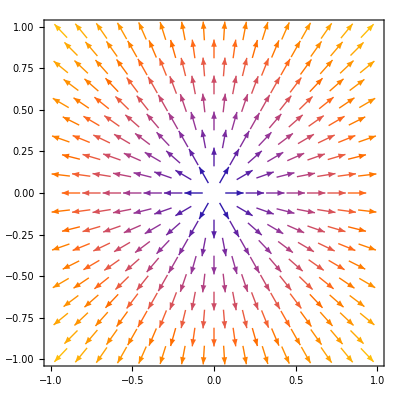

```mathematica
VectorPlot[{x, y},{x,-1,1}, {y, -1,1}]
```

```mathematica
VectorPlot[{x, y},{x,y}∈Region[Circle[]]]
```

VectorPlot::idomdim: {x,y}∈Region[Circle[]] does not have a valid dimension as a plotting domain.

```mathematica
VectorPlot[{x,y},{x,y}∈RegionIntersection[Disk[], Disk[0.8]]]
```

VectorPlot::idomdim: {x,y}∈RegionIntersection[Disk[],Disk[0.8]] does not have a valid dimension as a plotting domain.

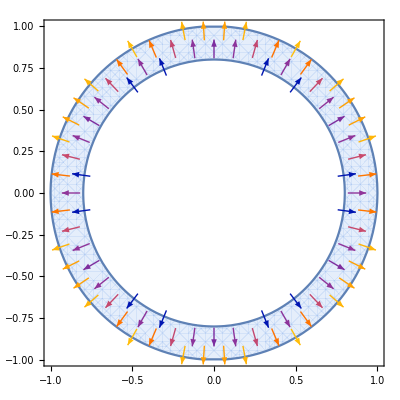

```mathematica
VectorPlot[{x,y},{x,y}∈Region[RegionDifference[Disk[{0,0}],Disk[{0,0},0.8]]]]
```

```mathematica
RegionIntersection[Disk[], Disk[0.8]]
```

```mathematica
Region[
RegionDifference[Disk[],Disk[0.8]]
]
```

Region::reg: RegionDifference[Disk[{0,0}],Disk[0.8]] is not a correctly specified region.

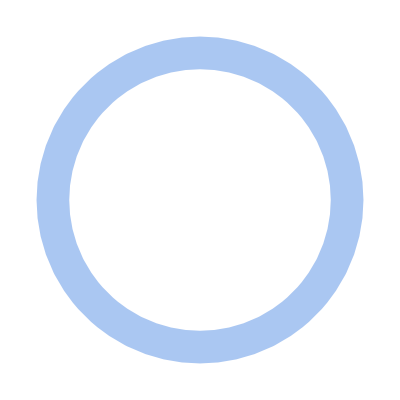

```mathematica
Region[RegionDifference[Disk[{0,0}],Disk[{0,0},0.8]]]
```

```mathematica
VectorPlot3D[ {x, y, z}, {x,y,z}∈Region[Ball[]]]
```

-Graphics3D-

```mathematica
Graphics3D[{ Opacity[0.3],Cone[{{0,0,1}, {0,0,0}},1]}]
```

-Graphics3D-

```mathematica
Show[%73, %64]
```

-Graphics3D-

```mathematica
Refine[Conjugate[{1,b}] .PauliMatrix[1] .{1,b}/.k->Sqrt[kx^2 + ky^2 + kz^2],
```

```mathematica
% * Refine[1/(1+Conjugate[b] b)/.k->Sqrt[kx^2 + ky^2 + kz^2], {k, kx, ky, kz}∈Reals]
```

Out[0]/(1+b Conjugate[b])

```mathematica
b=(k-kz)/(kx - I ky)
```

```mathematica
component[n_, b_]:=FullSimplify[Refine[Conjugate[{1,b}] .PauliMatrix[n] .{1,b} /(1+Conjugate[b] b)/.k->Sqrt[kx^2 + ky^2 + kz^2], {k, kx, ky, kz}∈Reals]
]
```

```mathematica
component[2, (-k-kz)/(ky - I kx)]
```

-kx/(√(kx^2+ky^2+kz^2))

```mathematica
Simplify[((-kz+√(kx^2+ky^2+kz^2))/(kx-ⅈ ky)+(-kz+√(kx^2+ky^2+kz^2))/(kx+ⅈ ky))/(1+((-kz+√(kx^2+ky^2+kz^2))^2)/((kx-ⅈ ky) (kx+ⅈ ky)))]
```

(kx (-kz+√(kx^2+ky^2+kz^2)))/(kx^2+ky^2+kz (kz-√(kx^2+ky^2+kz^2)))

```mathematica
FullSimplify[((-kz+√(kx^2+ky^2+kz^2))/(kx-ⅈ ky)+(-kz+√(kx^2+ky^2+kz^2))/(kx+ⅈ ky))/(1+((-kz+√(kx^2+ky^2+kz^2))^2)/((kx-ⅈ ky) (kx+ⅈ ky)))]
```

kx/(√(kx^2+ky^2+kz^2))

Are the states orhtogonal?

```mathematica
Conjugate[{1,(k-kz)/(kx - I ky)} ].{1,(-k-kz)/(kx - I ky)}
```

1+((-k-kz) (Conjugate[k]-Conjugate[kz]))/((kx-ⅈ ky) (Conjugate[kx]+ⅈ Conjugate[ky]))

```mathematica
Simplify[1+((-k-kz) (k-kz))/(kx-ⅈ ky)^2]
```

1+(-k^2+kz^2)/(kx-ⅈ ky)^2

```mathematica
Refine[%104, {k, kx, ky, kz}∈ Reals]/.k->Sqrt[kx^2 + ky^2 + kz^2]
```

1+((-kz-√(kx^2+ky^2+kz^2)) (-kz+√(kx^2+ky^2+kz^2)))/((kx-ⅈ ky) (kx+ⅈ ky))

```mathematica
Simplify[%]
```

0

```mathematica
Conjugate[(k-kz)/(kx - I ky)]*(-k-kz)/(kx - I ky)
```

((-k-kz) (Conjugate[k]-Conjugate[kz]))/((kx-ⅈ ky) (Conjugate[kx]+ⅈ Conjugate[ky]))

```mathematica
Refine[%, {k, kx, ky, kz}∈Reals]
```

((-k-kz) (k-kz))/((kx-ⅈ ky) (kx+ⅈ ky))

```mathematica
%/.k->Sqrt[kx^2+ ky^2 + kz^2]
```

((-kz-√(kx^2+ky^2+kz^2)) (-kz+√(kx^2+ky^2+kz^2)))/((kx-ⅈ ky) (kx+ⅈ ky))

```mathematica
Simplify[((-kz-√(kx^2+ky^2+kz^2)) (-kz+√(kx^2+ky^2+kz^2)))/((kx-ⅈ ky) (kx+ⅈ ky))]
```

-1